## Importing and definitions

```mathematica
Get[NotebookDirectory[]<>"../QMB.wl"]
```

```mathematica
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]]
```

```mathematica
Braket[a_,b_]:=Conjugate[a].b
```

```mathematica
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]]
```

```mathematica
MeanLevelSpacingRatioData=Import["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv","CSV"];
```

## Global parameters

```mathematica
(*Subscript[h, x]: magnetic field in x direction. L: number of spins*)
{hx,L}={1,11}
```

{1,11}

## Mean level spacing ratio (r_n)(h_z/h_x,J/h_x)

```mathematica
DateString[]
(*Parece que tarda 2.05~2.1 s por iteración, debería tardar approx 41 min*)
AbsoluteTiming[
Do[
Module[
{H,eigVals,eigVecs,EvenEigVals,hz,J},
{hz,J}=hzJ;
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
EvenEigVals=eigVals[[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]]];
AppendTo[MeanLevelSpacingRatioData,{hz,J,MeanLevelSpacingRatio[EvenEigVals]}];
],{hzJ,Tuples[Complement[Range[300],Range[5,300,5]]/100.,2]}
]
]
DateString[]
```

Fri 23 Aug 2024 17:38:16

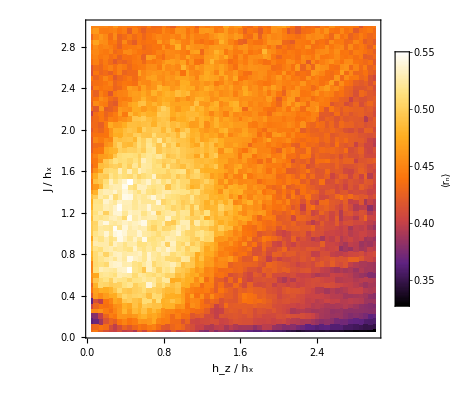

```mathematica
fontSize=18;
fig=
ListDensityPlot[MeanLevelSpacingRatioData,
InterpolationOrder->0,
ColorFunction->"SunsetColors",
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}]
```

```mathematica
Select[MeanLevelSpacingRatioData,#[[1]]==0.5&]
```

{{0.5,0.05,0.392313},{0.5,0.1,0.43143},{0.5,0.15,0.445958},{0.5,0.2,0.464501},{0.5,0.25,0.486684},{0.5,0.3,0.492728},{0.5,0.35,0.492674},{0.5,0.4,0.506533},{0.5,0.45,0.502572},{0.5,0.5,0.502211},{0.5,0.55,0.518218},{0.5,0.6,0.511052},{0.5,0.65,0.520384},{0.5,0.7,0.518807},{0.5,0.75,0.535035},{0.5,0.8,0.53132},{0.5,0.85,0.53804},{0.5,0.9,0.529142},{0.5,0.95,0.536659},{0.5,1.,0.528383},{0.5,1.05,0.533532},{0.5,1.1,0.535304},{0.5,1.15,0.52709},{0.5,1.2,0.531649},{0.5,1.25,0.523139},{0.5,1.3,0.522423},{0.5,1.35,0.521708},{0.5,1.4,0.52383},{0.5,1.45,0.512939},{0.5,1.5,0.525955},{0.5,1.55,0.5208},{0.5,1.6,0.513399},{0.5,1.65,0.523985},{0.5,1.7,0.51727},{0.5,1.75,0.513381},{0.5,1.8,0.502773},{0.5,1.85,0.49696},{0.5,1.9,0.483938},{0.5,1.95,0.501116},{0.5,2.,0.491369},{0.5,2.05,0.489944},{0.5,2.1,0.494728},{0.5,2.15,0.470981},{0.5,2.2,0.47677},{0.5,2.25,0.47702},{0.5,2.3,0.466838},{0.5,2.35,0.468723},{0.5,2.4,0.462706},{0.5,2.45,0.437249},{0.5,2.5,0.434232},{0.5,2.55,0.433523},{0.5,2.6,0.44016},{0.5,2.65,0.443656},{0.5,2.7,0.441459},{0.5,2.75,0.447117},{0.5,2.8,0.444674},{0.5,2.85,0.423355},{0.5,2.9,0.434046},{0.5,2.95,0.448051},{0.5,3.,0.444259}}

```mathematica
(Tuples[Complement[Range[300],Range[5,300,5]]/100.,2]//Length)*1.6/3600
```

25.6

## Export data and figure

```mathematica
(*Data*)
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/mean_level_spacing_ratio.csv",Prepend[MeanLevelSpacingRatioData,{"h_z/h_x","J/h_x","<r_n>"}],"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/mean_level_spacing_ratio.csv

```mathematica
(*Figure*)
Export["/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png",fig,"PNG",ImageResolution->300]
```

/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png